# d-orb./s-orb. ratio plotting

This is how I got rescaling coefficient of 0.2 for d-orbitals used in PP-STM code. It is from d/s ratio plotted in this notebook. It is approximate average far away d/s ratio for basis valence functions used in FHI-AIMS.
This factor is important to lower down contributions from d-orbitals which do not protrude that much into vacuum.
FHI-AIMS was chosen since it has very well defined basis-set which should be closest to real hydrogen-like basis.

```mathematica
atomicprop=Import["~/Documents/atomic_prop.dat","Table"];
path="~/Documents/WORK/AIMS_calc/WF_ploting/6th_row/";
tmp1=Import[path<>"geometry.in","Table"];
bas1={};a0=0;
For[i=1,i≤Length[tmp1],i++,If[tmp1[[i,1]]=="atom",{bas1=Append[bas1,{tmp1[[i,5]],tmp1[[i,2]],tmp1[[i,3]],tmp1[[i,4]]}],a0+=1}]];tmp1=.;
maxat1=a0;
species=bas1[[All,1]];
species//TableForm
atoms=Array[Null,maxat1];
For[i=1,i≤maxat1,i++,For[j=1,j≤99,j++,If[ToString[bas1[[i,1]]]==ToString[atomicprop[[j,1]]],atoms[[i]]={j,bas1[[i,1]],bas1[[i,2]](**rescale*),bas1[[i,3]](**rescale*),bas1[[i,4]](**rescale*),atomicprop[[j,2]],atomicprop[[j,4]],atomicprop[[j,5]],atomicprop[[j,6]]}]]]
Graphics3D[Rotate[Table[Tooltip[{RGBColor[atoms[[i,{7,8,9}]]/256],Sphere[atoms[[i,{3,4,5}]],0.6*atoms[[i,6]]]},{i,atoms[[i,{2,3,4,5}]]}],{i,1,maxat1}],0 Degree,{0,0,1}],Lighting->"Neutral",ViewPoint->20000. {0,-1,0},ImageSize->80,Axes->False,Boxed->False]
```

W
Ir
Pt
Au

-Graphics3D-

```mathematica
R=.;
species
lmax={1,2,2,3,3,3,4};
o[1]:="_s.dat"
o[2]:="_p.dat"
o[3]:="_d.dat"
For[i=1,i≤Length[species],i++,{n[i_]:=ElementData[species[[i]],"Period"]}]
name[i_,k_,l_]:=If[l<3,path<>"/at_"<>ToString[i]<>"_"<>ToString[k]<>"_"<>ToString[n[i]]<>o[l],path<>"/at_"<>ToString[i]<>"_"<>ToString[k]<>"_"<>ToString[n[i]-1]<>o[l]];

For[i=1,i≤Length[species],i++,{For[l=1,l≤lmax[[n[i]]],l++,{(*Print[name[i,I,l]],*)For[k=1,k≤100,k++,If[FileExistsQ[name[i,k,l]],{Print[name[i,k,l]],R[i,l]=Import[name[i,k,l],"Table",HeaderLines->1]}]]}]}]
```

{W,Ir,Pt,Au}

~/Documents/WORK/AIMS_calc/WF_ploting/6th_row//at_1_6_6_s.dat

~/Documents/WORK/AIMS_calc/WF_ploting/6th_row//at_1_15_5_d.dat

~/Documents/WORK/AIMS_calc/WF_ploting/6th_row//at_2_25_6_s.dat

~/Documents/WORK/AIMS_calc/WF_ploting/6th_row//at_2_34_5_d.dat

~/Documents/WORK/AIMS_calc/WF_ploting/6th_row//at_3_44_6_s.dat

~/Documents/WORK/AIMS_calc/WF_ploting/6th_row//at_3_53_5_d.dat

~/Documents/WORK/AIMS_calc/WF_ploting/6th_row//at_4_63_6_s.dat

~/Documents/WORK/AIMS_calc/WF_ploting/6th_row//at_4_72_5_d.dat

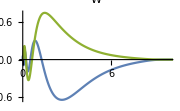
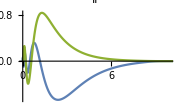
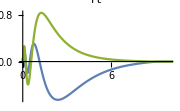
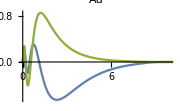

```mathematica
Table[{ListLinePlot[Table[R[i,l],{l,1,lmax[[n[i]]]}],PlotRange->{{0,10},All},PlotLabel->species[[i]],LabelStyle->Directive[Black,8],ImageSize->Small,PlotLegends->{"s","p","d"}]},{i,1,Length[species]}]//TableForm
```

{{-0.443231,-0.426034,-0.427125,-0.428175,Indeterminate},{-0.270829,-0.220387,-0.206845,-0.204792,Indeterminate},{-0.275399,-0.228983,-0.217082,-0.215346,Indeterminate},{-0.237606,-0.188081,-0.174686,-0.172603,Indeterminate}}

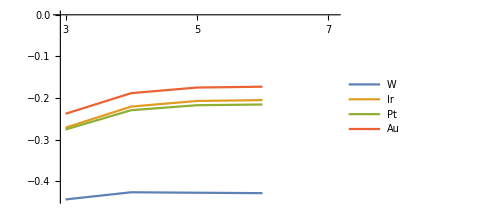

```mathematica
aB=1.889725989;(*Angstrom to Bohr radius*)
n4={};
n5={};
n6={};
n7={};
n8={};
Table[{For[j=1,j≤Length[R[i,1]],j++,If[R[i,1][[j,1]]<3.0*aB,tmp4=j,If[R[i,1][[j,1]]<4.0*aB,tmp5=j,If[R[i,1][[j,1]]<5.0*aB,tmp6=j,If[R[i,1][[j,1]]<6.0*aB,tmp7=j,If[R[i,1][[j,1]]<7.0*aB,tmp8=j]]]]]],n4=Append[n4,tmp4],n5=Append[n5,tmp5],n6=Append[n6,tmp6],n7=Append[n7,tmp7],n8=Append[n8,tmp8]},{i,1,Length[species]}];
(*{n4,n5,n6,n7,n8}*)
(*"d/s ratio";*)
species
div=Table[{R[i,3][[n4[[i]],2]]/R[i,1][[n4[[i]],2]],R[i,3][[n5[[i]],2]]/R[i,1][[n5[[i]],2]],R[i,3][[n6[[i]],2]]/R[i,1][[n6[[i]],2]],R[i,3][[n7[[i]],2]]/R[i,1][[n7[[i]],2]],R[i,3][[n8[[i]],2]]/R[i,1][[n8[[i]],2]]},{i,1,Length[species]}]
ListLinePlot[div,PlotRange->{{0.9,5.1},All},ImageSize->Medium,PlotLegends->Table[species[[i]],{i,1,Length[species]}],Ticks->{Table[{i,i+2},{i,1,7}],Automatic}]
```

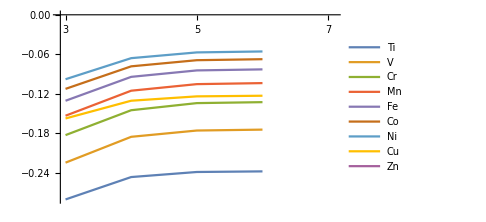

```mathematica
(*4TH ROW; 3-7 Angstrom (originally in Borh radii))*)
{{-0.2801435087805844,-0.2461805895860931,-0.23849761674752165,-0.23757368515349458,Indeterminate},{-0.2243263776683928,-0.18513056819003626,-0.17559723419436457,-0.17422055449159968,Indeterminate},{-0.1825523411495038,-0.14478585211512932,-0.13399814379650177,-0.13253871420600744,Indeterminate},{-0.1531326092400517,-0.1151837529516369,-0.10520295386182124,-0.10363980430695396,Indeterminate},{-0.13042111956926866,-0.09416058398534254,-0.08438873860790062,-0.08281000809714402,Indeterminate},{-0.1123942856287139,-0.07820520092870693,-0.06888906583213937,-0.06736099420430287,Indeterminate},{-0.09777004830681256,-0.06579378439795425,-0.0570680608567388,-0.05563218572841743,Indeterminate},{-0.15729991219935532,-0.1303718444864746,-0.1237593375552344,-0.12280826905645387,Indeterminate},{(R[9,3]⟦{1149,1152,1156,1159,1162,1165,1168,1171}⟦9⟧,2⟧)/(R[9,1]⟦{1149,1152,1156,1159,1162,1165,1168,1171}⟦9⟧,2⟧),(R[9,3]⟦{1172,1176,1179,1183,1186,1189,1192,1195}⟦9⟧,2⟧)/(R[9,1]⟦{1172,1176,1179,1183,1186,1189,1192,1195}⟦9⟧,2⟧),(R[9,3]⟦{1190,1194,1198,1201,1204,1207,1210,1213}⟦9⟧,2⟧)/(R[9,1]⟦{1190,1194,1198,1201,1204,1207,1210,1213}⟦9⟧,2⟧),(R[9,3]⟦{1205,1209,1212,1216,1219,1222,1225,1228}⟦9⟧,2⟧)/(R[9,1]⟦{1205,1209,1212,1216,1219,1222,1225,1228}⟦9⟧,2⟧),(R[9,3]⟦{1218,1222,1225,1228,1232,1235,1238,1241}⟦9⟧,2⟧)/(R[9,1]⟦{1218,1222,1225,1228,1232,1235,1238,1241}⟦9⟧,2⟧)}}
```

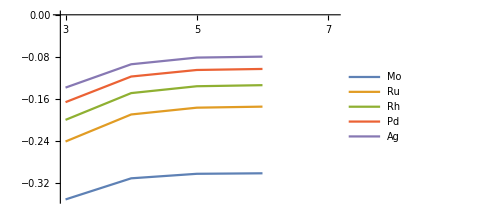

```mathematica
(*5TH ROW*)
{{-0.35035281826217074,-0.3102758888325367,-0.3017053395930674,-0.3007569850534154,Indeterminate},{-0.24041551075006282,-0.18913481006691102,-0.1762443107722583,-0.17427486859916763,Indeterminate},{-0.19937249482197295,-0.1485796997820161,-0.13556934066751972,-0.13353470799809597,Indeterminate},{-0.1657773945051138,-0.11714557362241426,-0.10471075654167186,-0.10276249443283637,Indeterminate},{-0.1381568259098598,-0.09386835932846183,-0.08119535314979708,-0.07939929972945833,Indeterminate}}
```

```mathematica
(*6TH ROW*)
{{-0.44323130503066155,-0.42603393553119073,-0.42712547482045204,-0.42817463771705205,Indeterminate},{-0.2708290495121187,-0.22038709972324197,-0.2068453697683175,-0.2047918588388887,Indeterminate},{-0.27539942953631563,-0.22898301361226783,-0.21708245842486992,-0.21534565138184164,Indeterminate},{-0.23760563925738018,-0.18808113106400562,-0.17468551779592725,-0.17260293173238136,Indeterminate}}
```

```mathematica
(* OLD Results *)
```

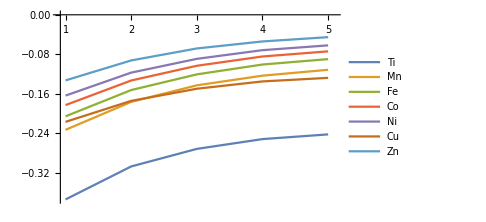
```mathematica
(*1st_run*)
(*"d/s ratio";*)
{{-0.3746236361729733,-0.30768685207492297,-0.2720734903748831,-0.2522100421802782,-0.24263827748051076},{-0.23339739682016764,-0.17668256193637735,-0.14309585958665005,-0.12350543561418324,-0.11159238237895264},{-0.20598145294640904,-0.15270796325145491,-0.12088715992867825,-0.10089518989917752,-0.08993229405614099},{-0.18318235086187348,-0.13332856838118942,-0.10342642267301737,-0.08457984945110428,-0.07418750718822237},{-0.16390761341376844,-0.11734828804254137,-0.08938339417486355,-0.0717579084537657,-0.06203322647484005},{-0.21722969570581654,-0.17463532883287755,-0.15002609507232448,-0.1351834576257597,-0.1279405621758133},{-0.13309555809593546,-0.09259074464327481,-0.06831380264121391,-0.05407912525134909,-0.04534994193704059}}
-Graphics-
```

{{-0.355335,-0.273427,-0.226584,-0.198338,-0.18347},{-0.310898,-0.231664,-0.185764,-0.159547,-0.143881},{-0.277477,-0.196689,-0.152745,-0.12764,-0.112657},{-0.24364,-0.170571,-0.128243,-0.102421,-0.0885127},{-0.37412,-0.30145,-0.257659,-0.231625,-0.215504},{-0.374455,-0.304394,-0.26308,-0.23911,-0.224641}}

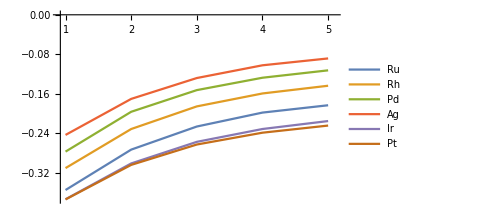

```mathematica
(*2nd_run*)
(*"d/s ratio";*)
{"Ru","Rh","Pd","Ag","Ir","Pt"}
```

{{-0.338701,-0.267623,-0.224686,-0.199127,-0.183271}}

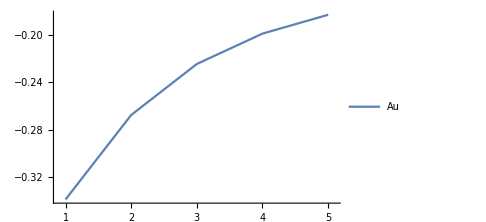

```mathematica
(*3nd_run*)
(*"d/s ratio";*)
{"Au"}
```